```mathematica
F[Ω_,z_]:=Integrate[1/(Ω(1+x)^3+(1-Ω)(1+x)^(3/2))^(1/2),{x,0,z},Assumptions->{z>0&&z<1}];
```

```mathematica
a1=Plot[F[0,z],{z,0,1},AxesLabel->{"z","F[Ω,z]"},PlotLabel-> "Ω=0",PlotRange->{{0,1},{0,1}}];
a2=Plot[F[0.3,z],{z,0,1},AxesLabel->{"z","F[Ω,z]"},PlotLabel-> "Ω=0.3",PlotRange->{{0,1},{0,1}}];
a3=Plot[F[0.7,z],{z,0,1},AxesLabel->{"z","F[Ω,z]"},PlotLabel-> "Ω=0.7",PlotRange->{{0,1},{0,1}}];
a4=Plot[F[1,z],{z,0,1},AxesLabel->{"z","F[Ω,z]"},PlotLabel-> "Ω=1",PlotRange->{{0,1},{0,1}}];
```

```mathematica
GraphicsColumn[{a1,a2,a3,a4}];
```

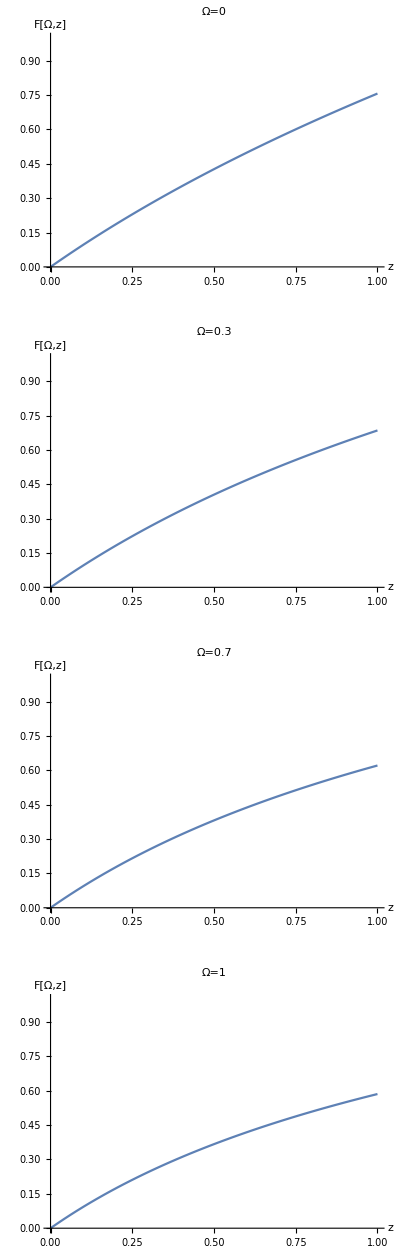

```mathematica
%136
```

```mathematica
%119
```

```mathematica
(* Ω=0 analytic result *)
Integrate[1/(1+x)^(3/4),{x,0,z}];
```

```mathematica
ConditionalExpression[-4+4 (1+z)^(1/4),Re[z]>-1||z∉Reals]
```

ConditionalExpression[-4+4 (1+z)^(1/4), Re[z]>-1||z∉ℝ]

```mathematica
a5=Plot[-4+4(1+z)^(1/4),{z,0,1},AxesLabel->{"z","F[Ω,z]"},PlotLabel-> "Ω=0 analytic",PlotRange->{{0,1},{0,1}}];
```

```mathematica
(* Ω=1 analytic result *)
Integrate[1/(1+x)^(3/2),{x,0,z}];
```

```mathematica
ConditionalExpression[2-2/(√(1+z)),Re[z]>-1||z∉Reals]
```

ConditionalExpression[2-2/(√(1+z)), Re[z]>-1||z∉ℝ]

```mathematica
a6=Plot[2-2/(1+z)^(1/2),{z,0,1},AxesLabel->{"z","F[Ω,z]"},PlotLabel-> "Ω=1 analytic",PlotRange->{{0,1},{0,1}}];
```

```mathematica
%126
```

```mathematica
GraphicsColumn[{a5,a6}];
```

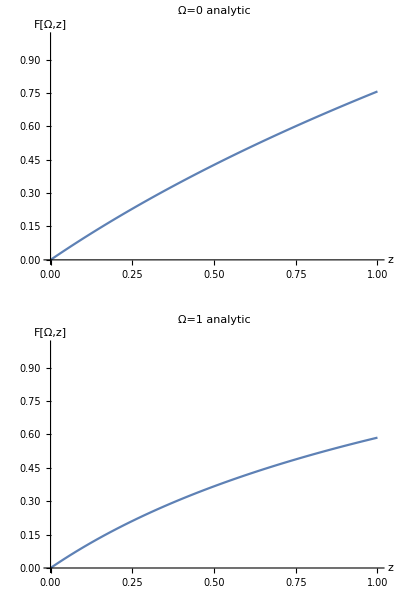

```mathematica
%128
```

```mathematica
a7=Plot[{-4+4(1+z)^(1/4),2-2/(1+z)^(1/2)},{z,0,1},AxesLabel->{"z","F[Ω,z]"},PlotLabel-> "Ω=1 and Ω=0 analytic",PlotLegends-> {"Ω=0","Ω=1"},PlotRange->{{0,1},{0,1}}];
```

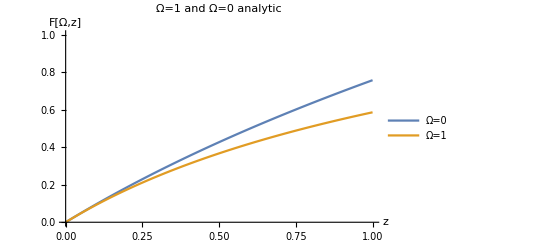

```mathematica
%134
```

```mathematica
a8=Plot[{F[0,z],F[0.3,z],F[0.7,z],F[1,z]},{z,0,1},AxesLabel->{"z","F[Ω,z]"},PlotLabel-> "Function for Ω=0,0.3,0.7,1",PlotLegends-> {"Ω=0","Ω=0.3","Ω=0.7","Ω=1"},PlotRange->{{0,1},{0,1}}];
```

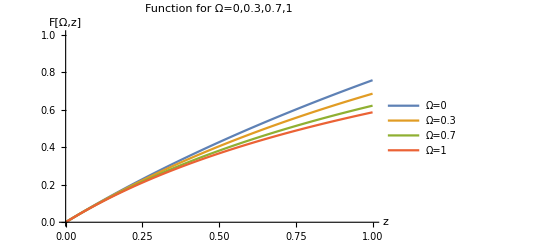

```mathematica
%139
```